```mathematica
SetDirectory[NotebookDirectory[]];
```

# Simulating traffic flow using a Cellular Automaton model.

## 1. Background

A Cellular Automaton is a discrete mathematical model, which consists of a grid of cells. Each cell is in one of a finite number of possible states at the initial timestep. At each timestep, the grid of cells is updated according to an update function applied to each cell. The result of the update function depends on the current state of the cell, and the states of the cells in its neighbourhood. At the next timestep the cell will be in the state resulting from the update function. Studies of CA have shown that very simple update functions can give rise to remarkable complexity.

## 2. Introduction

## 3. Method

In this project, a one-dimensional cellular automaton model is used to simulate traffic flow.
The model starts with a road consisting of n number of cells. Cars are randomly placed in the cells, such that the density of traffic, given by (Number of cars / n) matches the specified value. 
Then each car gets assigned a starting speed randomly selected between 1 and the specified maximum speed v_max.  The speed of each car specifies how many cells it has advanced from left to right in the previous timestep. From the point of view of the simulation it is irrelevant but interesting to note, that the initial speeds of the cars are randomly generated, and therefore might be unrealistic. This is corrected in the first iteration of the update function.

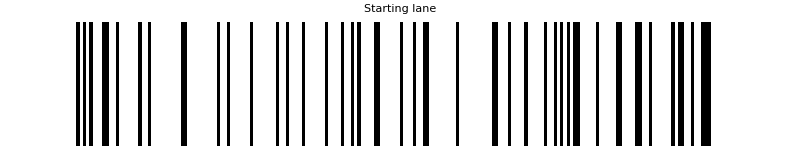

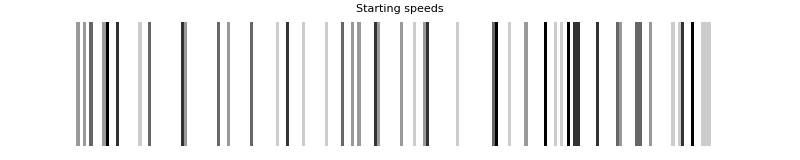

```mathematica
seed=Import["single_seed1.csv"];
ArrayPlot[{Table[seed[[i,1]],{i,1,Length[seed]}]},ImageSize->800,PlotLabel->"Starting lane"]
ArrayPlot[{Table[seed[[i,2]],{i,1,Length[seed]}]},ImageSize->800,PlotLabel->"Starting speeds"]
```

The state of the road is then updated according to the following update function being applied to each car:

1 - If the speed v of the car is lower than v_max, increase the speed by one to v+1.
2 - If a driver of a car at position i sees the next vehicle at position (i + j), and j < v, the driver reduces the speed v to j - 1 in order to avoid collision.
3 - If the speed v of a car is greater than zero, its speed is reduced by one to v - 1 with a probability p.
4 - Each car advances by v sites.

Step 1 mimics the tendency of real drivers who, when the traffic allows, aim to travel at the maximum allowed speed v_max.
Step 2 is where all the cars adjust their speeds to avoid collisions. It is important to note, that the resulting speed of each car only depends on the state of the road in the current timestep. The drivers only look ahead until the position of the car in front of them, and no further. They do not attempt to predict how many sites the car in front would advance, but instead they always change their speed to avoid collision even if the car in front remains stationary. The choice of such a seemingly unnatural update step might seem counterintuitive but, as we will later see, it leads to realistic simulations of traffic jams and stop-and-go traffic.
Step 3 introduces an element of randomness to the model, where each car has a small probability p to slow down by a small amount. This step, surprisingly, mimics the behaviour of human drivers on real roads. In reality, there might be many reasons for such a slowdown - dodging a pothole, waning attention of the driver, a gust of headwind, etc. Later on these miniscule effects lead to a buildup of traffic on roads, and may cause huge traffic jams.
Step 4 updates the state of the road, with each car advancing by v sites. This step assumes a circular road, with cars leaving at the end of the road appearing at the beginning again with the same speed. This keeps the density of the traffic constant, and counters probabilistic effects arising from new cars being fed in the beginning of the road with randomised speeds.

The update function outputs a road in the same format as the original, therefore NestList can be used to generate a desired number of consecutive updates on the same road. A simple animation can show how the traffic evolves over time.

```mathematica
createLaneAnimation[trafficin_List]:=Animate[ArrayPlot[{Table[trafficin[[i,j,1]],{j,1,Length[trafficin[[1]]]}]},ImageSize->600],{i,1,Length[trafficin],1},AnimationRunning->False];
traffic1=ToExpression[Import["single_traffic1.csv"]];
createLaneAnimation[traffic1]
```

This simulation shows a buildup of traffic at some points of the road, where cars bunch up behind each other and come to a halt. Then after a while, when the car in front of them starts moving, they gradually accelerate and resume traveling at a normal pace.
This behaviour is the same as seen on many motorways worldwide. Small disturbances in the speed of some cars causes the car behind them to brake a little bit harder to make sure they avoid collision. Then the car behind them brakes yet a little harder, until some of the cars end up stopping, and bunching up behind each other. This result might seem counterintuitive, but surprisingly, it is very realistic. In cases when there are no lane closures or accidents, this mechanism is responsible for most of the highway traffic jams, and roads developing stop-and-go traffic in the morning rush hours, even though seemingly there is no reason for them.
The main point of this report is to investigate the behaviour of traffic flow and the occurrence of traffic jams, and gain an insight what parameters affect the evolution of traffic and how.

## 4. Single lane traffic

Only 1 type of vehicle

Firstly, we can investigate for a given maximum speed, how the density of the traffic affects the shape of traffic jams. The 2D plots below show the evolution of traffic for 6 densities, ranging from 10% to 35% of the cells in the road being occupied. The plots show the starting occupancy of the road in the first row, and each row below shows a consecutive iteration of the update function being applied to the road.

```mathematica
createArrayPlot[trafficin_List,pixelsize_]:=ArrayPlot[Table[trafficin[[i,j,1]],{i,1,Length[trafficin]},{j,1,Length[trafficin[[1]]]}],ImageSize->600,PixelConstrained->pixelsize];
trafficTables=ToExpression[Import["traffic_tables1.csv"]];
Table[createArrayPlot[trafficTables[[i]],1],{i,1,6}];

kukk=Table[ArrayPlot[Table[trafficTables[[n,i,j,1]],{i,1,Length[trafficTables[[1]]]},{j,1,Length[trafficTables[[1,1]]]}],ImageSize->600,PixelConstrained->1,PlotLabel->"density ="+(0.05n)],{n,1,Length[trafficTables]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["kukk6.jpg",kukk[[6]]]
```

kukk6.jpg

In the plots we can see that for low density, all the cars are able to travel at the maximum allowed speed on the road, and there are no buildups of cars anywhere. As the density increases, more and more cars are forced to reduce their speed to avoid collisions with the car in front. In the 3rd plot at 20% density, we see one single traffic jam where cars coming from behind have to reduce their speed drastically until they get through the congestion, but after they are able to accelerate and continue their journey at close to the maximum allowed speed.
An interesting aspect to investigate next is how the total throughput of the road, that is the average of how many tiles do all the cars advance in each iteration of the simulation. In this sense, the throughput is analogous to the flux of cars passing thorough the road. Measuring the throughput would give us a measure to quantify the effects of the traffic jams, and their impact on commuters. It is important to note that since the initial state of the road, and the instances when cars are breaking are randomly generated, we need to run the simulation multiple times and average the outcome to get a more reliable result. For the following plot, each simulation was ran 10 times, with a road length of track=200 and a brake probability of p=0.1 over 200 iterations. The density of traffic was varied between 0.05 to 0.35 in steps of 0.01.

```mathematica
singleThrough=Flatten[Import["single_throughput.csv"]];
Dimensions[singleThrough]
singleThroughPlot=ListPlot[Transpose[{Table[0.01i,{i,1,50}],singleThrough}],Joined->True,AxesLabel->{"density of traffic","throughput of road"},PlotLegends->LineLegend[{Blue},{"average throughput"}]];
Export["pepe.jpg",Show[{singleThroughPlot,
Plot[i*200*5,{i,0.01,0.50},PlotStyle->Orange,PlotLegends->LineLegend[{Orange},{"linear fit"}]]}]]
```

{50}

pepe.jpg

The shape of the graph matches what we would expect based on the 6 plots showing the traffic for different densities (!!!reference?). At low densities, where all the cars travel at the maximum speed v_max, we see a linear increase of throughput with traffic density. The slope of the line is the max speed all the cars travel at, times the length of the road. These low density results will be said to be in the “linear regime”, where increasing the density of traffic results in a linear increase of throughput. This also matches the predictions of fluid-dynamics based traffic simulations, where the linear regime corresponds to laminar flow of cars.
The graph shows a sharp cutoff at a certain density, where the total throughput of the road starts to decrease with new cars being added to the road. This happens above the critical density, where cars start piling up behind each other. The higher the density, the more time cars spend in stop-and-go traffic with a very low average speed, therefore reducing the throughput.

Another interesting aspect to investigate is the average speed of the vehicles in the same traffic as before. We can get the value of average speed by dividing the total throughput by the number of cars. This is an important factor for most motorists on the road, as if the speed of the cars is decreased, they will feel as there is a traffic jam, even though the throughput of the road with more cars added is still increasing.

{50}

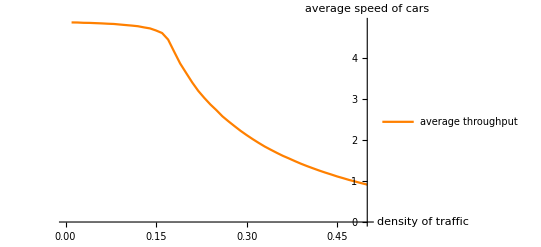

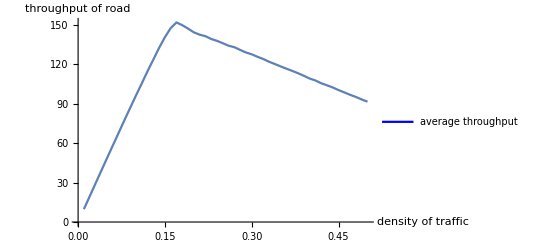
-Graphics--Graphics-

```mathematica
singleSpeeds=Flatten[ToExpression[Import["single_speeds.csv"]]];
Dimensions[singleSpeeds]
singleSpeedsPlot=ListPlot[Transpose[{Table[0.01i,{i,1,50}],singleSpeeds}],Joined->True,AxesLabel->{"density of traffic","average speed of cars"},AxesOrigin->{0.5,0},PlotStyle->Orange,PlotLegends->LineLegend[{Orange},{"average throughput"}]]
Overlay[{singleThroughPlot,singleSpeedsPlot}]
singleThroughPlot;
```

```mathematica
Export["bazmeg.jpg",Show[{ListPlot[Transpose[{Table[0.01i,{i,1,50}],singleSpeeds*30}],Joined->True,PlotStyle->Orange,ImageSize->Large,AxesLabel->{"density of traffic","average speed of cars"},PlotLegends->LineLegend[{Orange},{"average speed"}]],singleThroughPlot}]]
```

bazmeg.jpg

```mathematica
mash=Overlay[{ListPlot[Transpose[{Table[0.01i,{i,1,50}],singleSpeeds}],Joined->True,AxesLabel->{"","average speed of cars"},AxesOrigin->{0.5,0},ImagePadding->60,PlotStyle->Orange,ImageSize->Large,PlotLegends->Placed[LineLegend[{Orange},{"average speed"}],{1,.4}]],ListPlot[Transpose[{Table[0.01i,{i,1,50}],singleThrough}],Joined->True,AxesLabel->{"density of
 traffic","throughput of road"},ImagePadding->60,ImageSize->Large,PlotLegends->Placed[LineLegend[{Blue},{"throughput       "}],{1,.5}]]}]
```

-Graphics--Graphics-

In this plot the average throughput of the road, and a scaled up version of average speed is shown, It clearly seems that they both begin to fall at the same point when the road reaches its critical density. Based on this result we can also make the decision to only investigate the average throughput of the road, as the average speed of cars starts to fall at the same value of road parameters.
The point of further investigation is to see how the critical density varies with different parameters of the road, which will be measured by plotting the throughput of the road as a function of the investigated parameters.

A large source of randomness in the simulations is the fact that cars brake with a certain probability in each timestep. For this reason it is worth investigating how the throughput of the road changes with the brake probability, at different densities.

```mathematica
brakes=ToExpression[Import["brakes.csv"]];
ListPlot3D[brakes,ImageSize->Large,AxesLabel->{"brake probability","density of traffic","throughput of the road"},InterpolationOrder->1,ViewPoint->{1, -2, 1.2}]
Export["brakes.jpg",ListPlot3D[brakes,ImageSize->Large,AxesLabel->{"brake probability","density of traffic(%)","throughput of the road"},InterpolationOrder->1,ViewPoint->{1, -2, 1.2}]]
```

-Graphics3D-

brakes.jpg

This plot shows that the critical density does not change significantly while varying the brake probability from 0 to 30%. The only noticeable change is the reduction in throughput, as cars travelling at their normal maximum speed brake more often, thus reducing the average speed of cars on the road.

```mathematica
speedplot=Import["kecc.csv"];

ListPlot3D[speedplot,PlotTheme->"Scientific",ImageSize->Large,AxesLabel->{"maximum speed of vehicles","density of traffic (%)","throughput of the road"},InterpolationOrder->4,ViewPoint->{2, -2, 1.5}]
```

-Graphics3D-

```mathematica
Dimensions[speedplot]
```

```mathematica
sp=Transpose[speedplot];
spp=Show[Table[ListPlot[sp[[i]],PlotLabels->i,Joined->True,PlotStyle->RGBColor[0.1 i,.8-0.1i,1-0.1i],ImageSize->Large,AxesLabel->{"density of
 traffic","throughput of road"},ImagePadding->60],{i,1,8}],PlotRange->All]
Export["spp.jpg",spp]
```

-Graphics-

spp.jpg

```mathematica
Export["kek.jpg",ListPlot3D[speedplot,PlotTheme->"Scientific",ImageSize->Large,AxesLabel->{"maximum speed of vehicles","density of traffic (%)","throughput of the road"},InterpolationOrder->4,ViewPoint->{2, -2, 1.5}]]
```

kek.jpg

{11.7461,23.4488,25.4699,33.9165,40.9298,48.809,57.1035,64.0654,71.7694,78.9984,86.6535,94.29,101.218,105.098,115.843,123.097,130.273,136.349,142.094,144.98,142.913,141.33,138.833,137.875,136.151,134.111,132.518,130.813,129.251,127.39,125.743,123.712,121.416,120.186,118.826,116.302,114.949,113.42,111.239,109.576,107.673,105.879,103.931,102.489,100.542,98.7676,96.7281,95.0355,93.2527,91.5306}

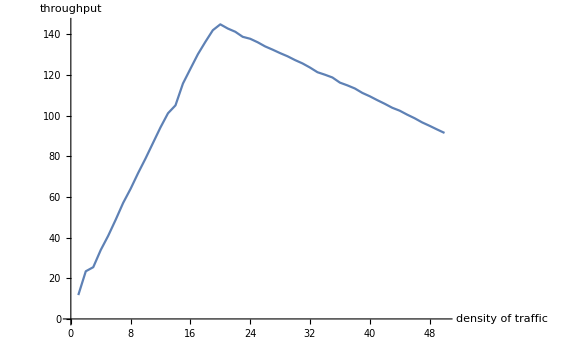

pff.jpg

```mathematica
typeTraffs=Flatten[ToExpression[Import["type_traffic_dendsity.csv"]]]
pff=ListPlot[typeTraffs,Joined->True,ImageSize->Large,AxesLabel->{"density of traffic","throughput"}]
Export["pff.jpg",pff]
```

```mathematica
ggwp=Import["type_traffic_ratio_dendsity.csv"];
gagg=ListPlot3D[ggwp,ImageSize->Large,AxesLabel->{"ratio of trucks","density","throughput"},ViewPoint->{1.5, -2, 1}]
Export["gagg.jpg",gagg]
```

-Graphics3D-

gagg.jpg